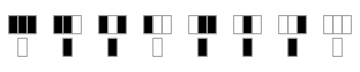
-Graphics--Graphics-
-Graphics-

```mathematica
multi=ResourceFunction["MultiwaySystem"];
render="StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->30],#1,#3]&);
statesGraph=multi[CellularAutomaton[110],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->{500,500}];
Column[{Row[{
ArrayPlot[CellularAutomaton[110,RandomInteger[1,200],200],ImageSize->{500,500}],statesGraph
}],
RulePlot[CellularAutomaton@110,ImageSize->Medium]},Alignment->Center]
```

```mathematica
confluentQ[graph_] := AllTrue[WeaklyConnectedGraphComponents[graph],
	Function[cc, AnyTrue[VertexList[cc], ContainsExactly[VertexInComponent[cc, #], VertexList[cc]] &]]]
totalConfluentQ[graph_] := CompleteGraphQ[TransitiveClosureGraph[graph]]
Column@Table[Row[{multiwayGraph=ResourceFunction["MultiwaySystem"][CellularAutomaton[rule],Tuples[{0,1},5],1,"StatesGraph","StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->25],#1,#3]&),ImageSize->Medium],Column[{
Text["Rule: "<>ToString@rule],Text["Confluent: "<>ToString@confluentQ[multiwayGraph]],Text["Total Confluent: "<>ToString@totalConfluentQ[multiwayGraph]]}]},"\t"],{rule,{4,41}}]
```

-Graphics-Rule: 4
Confluent: False
Total Confluent: False
		-Graphics-Rule: 41
Confluent: True
Total Confluent: True

```mathematica
Table[{rule,totalConfluentQ@multi[CellularAutomaton[rule],Tuples[{0,1},5],1,"StatesGraphStructure"]},{rule,1,50}]
```

{{1,False},{2,False},{3,False},{4,False},{5,False},{6,False},{7,False},{8,False},{9,False},{10,False},{11,False},{12,False},{13,False},{14,False},{15,False},{16,False},{17,False},{18,False},{19,False},{20,False},{21,False},{22,False},{23,False},{24,False},{25,False},{26,False},{27,False},{28,False},{29,False},{30,False},{31,False},{32,False},{33,True},{34,False},{35,True},{36,False},{37,False},{38,False},{39,False},{40,False},{41,True},{42,False},{43,True},{44,False},{45,False},{46,False},{47,False},{48,False},{49,True},{50,False}}

```mathematica
With[{rule=4},Row[{"Rule "<>ToString@rule,ArrayPlot[CellularAutomaton[rule,RandomInteger[1,100],100],ImageSize->Medium],g=multi[CellularAutomaton[rule],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->Medium],confluentQ@g,totalConfluentQ@g},"\t"]]
```

Rule 4-Graphics--Graphics-FalseFalse

```mathematica
With[{rule=15},Row[{"Rule "<>ToString@rule,ArrayPlot[CellularAutomaton[rule,RandomInteger[1,100],100],ImageSize->Medium],g=multi[CellularAutomaton[rule],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->Medium],confluentQ@g,totalConfluentQ@g},"\t"]]
```

Rule 15-Graphics--Graphics-TrueFalse

```mathematica
With[{rule=30},Row[{"Rule "<>ToString@rule,ArrayPlot[CellularAutomaton[rule,RandomInteger[1,100],100],ImageSize->Medium],g=multi[CellularAutomaton[rule],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->Medium],confluentQ@g,totalConfluentQ@g},"\t"]]
```

Rule 30-Graphics--Graphics-TrueFalse

```mathematica
With[{rule=110},Row[{"Rule "<>ToString@rule,ArrayPlot[CellularAutomaton[rule,RandomInteger[1,100],100],ImageSize->Medium],g=multi[CellularAutomaton[rule],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->Medium],confluentQ@g,totalConfluentQ@g},"\t"]]
```

Rule 110-Graphics--Graphics-TrueFalse

```mathematica
Row[{multi[CellularAutomaton@30,Tuples[{0,1},5],1,"StatesGraphStructure"],SimpleGraph@multi[CellularAutomaton@30,Tuples[{0,1},5],3,"CausalGraphStructure"]}]
```

-Graphics--Graphics-